# Code for case study #2, a stochastic, discrete-time, stage-structured model of annual and perennial plants

The germinant survival probability is denoted s̃ in the main text, but for whatever reason, this symbol doesn’t work with mathematica’s symbolic math capabilities. In this notebook, sN is the germinant survival probability.

Table 1 in Appendix 3 corresponds to SN = 0.975 (species 1 is a long-lived perennial, just like the other species). Table 2 in Appendix 3 corresponds to sN = 0 (species 1 is an annual).  

Each simulation is run for 100,000 time steps (parameter tMax = 100000). Running through all simulations (all species, all 2-resident invasion scenarios) may take some time, approximately ~5 minutes on a laptop.  The invasion growth rates of species 2 and 3 are small, and environments are very correlated, so many time steps are required. 

Here, the limiting factors are is the density of germinants after the seed germination phase of each timestep, i.e., N(t) + G X(t). The scaling factors are still calculated using the regulating factors. However, instead of defining the storage effect as a sum (of scaled covariances between regulating factors and the environmental parameter), we define the storage effect using the covariance between the environmental parameter and comeptition parameter. These two approaches are equivalent in the limit of small environmental noise, but can differ in the real world. Calculating the storage effect with the competition parameter makes the computations marginally simpler, and is conventional in this sort of model (i.e., models where a linear combination o population densities decrement the per capita growth rate).

```mathematica
(* ctrl+a to select all, then shift+enter to run the whole notebook *)
SeedRandom[20]
```

## Write Equations, select parameters, and simulate to make sure that species can coexist

```mathematica
(* time-1 maps for seed density X, germinant density G, enviornmental parameters E, and a vector of perturbative shocks W. *)
X1tp1[{X1_,X2_,X3_,N1_,N2_,N3_,E1_,E2_,E3_, ϵ_}]:= X1 s1(1-G1) + (X1 G1 + N1) * Exp[E1] / (1+A[[1,1]](G1 X1+N1)+A[[1,2]](G2 X2+N2)+A[[1,3]] (G3 X3+N3))
N1tp1[{X1_,X2_,X3_,N1_,N2_,N3_,E1_,E2_,E3_, ϵ_}]:= (X1 G1 +N1) sN1
E1tp1[{X1_,X2_,X3_,N1_,N2_,N3_,E1_,E2_,E3_, ϵ_}]:=μ1 + θ1 (E1 -μ1)+Sqrt[1-θ1^2]ϵ[[1]]
X2tp1[{X1_,X2_,X3_,N1_,N2_,N3_,E1_,E2_,E3_,ϵ_}]:= X2 s2(1-G2) + (X2 G2 + N2) * Exp[E2] / (1+A[[2,1]](G1 X1+N1)+A[[2,2]](G2 X2+N2)+A[[2,3]] (G3 X3+N3))
N2tp1[{X1_,X2_,X3_,N1_,N2_,N3_,E1_,E2_,E3_, ϵ_}]:= (X2 G2 +N2) sN2
E2tp1[{X1_,X2_,X3_,N1_,N2_,N3_,E1_,E2_,E3_, ϵ_}]:=μ2 +θ2 (E2 -μ2)+Sqrt[1-θ2^2]ϵ[[2]]
X3tp1[{X1_,X2_,X3_,N1_,N2_,N3_,E1_,E2_,E3_, ϵ_}]:= X3 s3(1-G3) + (X3 G3 + N3) *  Exp[E3] / (1+A[[3,1]](G1 X1+N1)+A[[3,2]](G2 X2+N2)+A[[3,3]] (G3 X3+N3))
N3tp1[{X1_,X2_,X3_,N1_,N2_,N3_,E1_,E2_,E3_, ϵ_}]:= (X3 G3+N3) sN3
E3tp1[{X1_,X2_,X3_,N1_,N2_,N3_,E1_,E2_,E3_, ϵ_}]:=μ3 +θ3 (E3 -μ3)+Sqrt[1-θ3^2]ϵ[[3]]
ϵtp1[{X1_,X2_,X3_,N1_,N2_,N3_,E1_,E2_,E3_, ϵ_}]:=RandomVariate[MultinormalDistribution[{0,0,0},W]];
```

```mathematica
(* set parameter values *)
(* matrix of competition coefficients *)
A = {
{1,0.001,0.001},
{0.001,1,1.001},
{0.001,1.001,1}
};
(* autocorrelation parameters *)
θ1 = 0.9;θ2 = 0.9;θ3 =  0.9;
(* survival parameters *)
s1 = 0.9;s2 = 0.9;s3 =0.9;(* seed survival *)
sN1=0.001;sN2 = 0.975;sN3 =0.975;(* germinant survival *)
(* germination parameters *)
G1 =0.1;G2 = 0.1;G3 = 0.1;
(* mean of E parameters *)
μ1 = 4;μ2 = 4;μ3 =4;
(* noise scales *)
σ1 = 1;σ2 =1;σ3 = 1;
(* cross-species correlations *)
τ12 =-0.49;τ13 = -0.49;τ23 = -0.49;
sVec ={s1,s2,s3}; (* vector of survival params *)
sNVec ={sN1,sN2,sN3};
GVec ={G1,G2,G3};
W= {
{σ1 σ1 ,σ1 σ2 τ12 ,σ1 σ3 τ13},
{σ2 σ1 τ12,σ2 σ2 ,σ2 σ3 τ23},
{σ3 σ1 τ13,σ3 σ2 τ23,σ3 σ3}
};
```

```mathematica
(* mapping function for all variables *)
f[{X1_,X2_,X3_,N1_,N2_,N3_,E1_,E2_,E3_, ϵ_}]:={
X1tp1[{X1,X2,X3,N1,N2,N3,E1,E2,E3, ϵ}],
X2tp1[{X1,X2,X3,N1,N2,N3,E1,E2,E3, ϵ}],
X3tp1[{X1,X2,X3,N1,N2,N3,E1,E2,E3, ϵ}],
N1tp1[{X1,X2,X3,N1,N2,N3,E1,E2,E3, ϵ}],
N2tp1[{X1,X2,X3,N1,N2,N3,E1,E2,E3, ϵ}],
N3tp1[{X1,X2,X3,N1,N2,N3,E1,E2,E3, ϵ}],
E1tp1[{X1,X2,X3,N1,N2,N3,E1,E2,E3, ϵ}],
E2tp1[{X1,X2,X3,N1,N2,N3,E1,E2,E3, ϵ}],
E3tp1[{X1,X2,X3,N1,N2,N3,E1,E2,E3, ϵ}],
ϵtp1[{X1,X2,X3,N1,N2,N3,E1,E2,E3, ϵ}]}
```

```mathematica
(*simulation parameters*)
tMax= 100000;
burnIn = 5000;
plotTMax =5000;
X1Init=1;
X2Init=1;
X3Init =1;
N1Init=1;
N2Init=1;
N3Init =1;
ϵInit= {0,0,0};
initDens = 0.001;
```

### Make sure that all species can coexist together

```mathematica
(* all species can coexist together *)
res=Transpose[NestList[f,{X1Init,X2Init, X3Init,N1Init,N2Init, N3Init,0,0,0,ϵInit},plotTMax]];
```

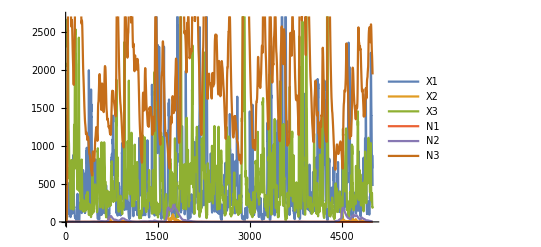

```mathematica
ListLinePlot[res[[1;;6,1;;plotTMax]],PlotLegends->{"X1","X2","X3","N1","N2","N3"}]
```

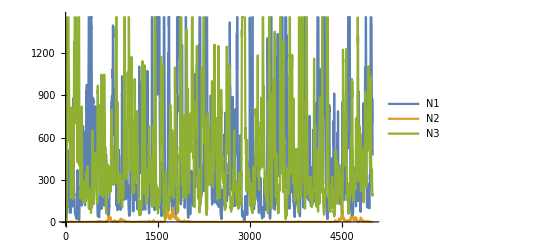

```mathematica
ListLinePlot[res[[1;;3,1;;plotTMax]],PlotLegends->{"N1","N2","N3"}]
```

```mathematica
(*res=Transpose[NestList[f,{X1Init,X2Init, X3Init,N1Init,N2Init, N3Init,0,0,0},200000]];*)
(* average densities of seeds*)
Map[Mean[#]&, res[[1;;3]]]
(* average densities of germinants*)
Map[Mean[#]&, res[[4;;6]]]
(* variance of environmental parameter E *)
Map[Variance[#]&, res[[7;;9]]]
```

{465.514,4.77518,510.558}

{0.0467898,18.5833,1976.13}

{1.13841,1.02491,1.09233}

### Make sure that all pairs of species can coexist. This means that the mutual invasibility criterion is applicable.

#### Consumers 1 and 2

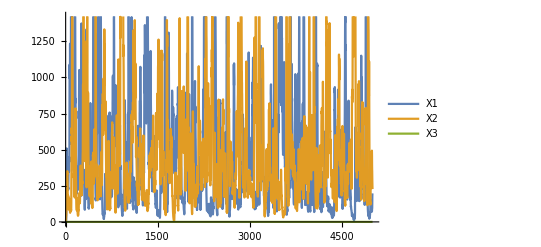

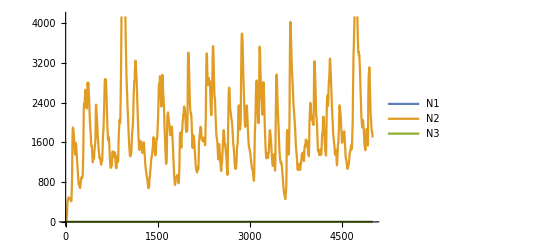

```mathematica
(* consumer 1 and 2 can coexist *)
res=Transpose[NestList[f,{X1Init,X2Init,0,N1Init,N2Init,0,0,0,0,ϵInit},plotTMax]];
ListLinePlot[res[[1;;3,1;;plotTMax]],PlotLegends->{"X1","X2","X3"}]
ListLinePlot[res[[4;;6,1;;plotTMax]],PlotLegends->{"N1","N2","N3"}]
```

```mathematica
(* average densities of seeds*)
Map[Mean[#]&, res[[1;;3]]]
(* average densities of germinants*)
Map[Mean[#]&, res[[4;;6]]]
(* variance of environmental parameter E *)
Map[Variance[#]&, res[[7;;9]]]
```

{432.46,488.971,0.}

{0.043486,1893.72,0.}

{0.971462,0.995165,1.12831}

#### Consumers 1 and 3

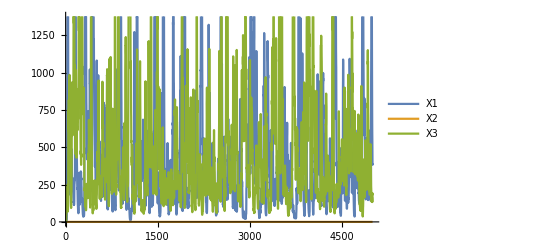

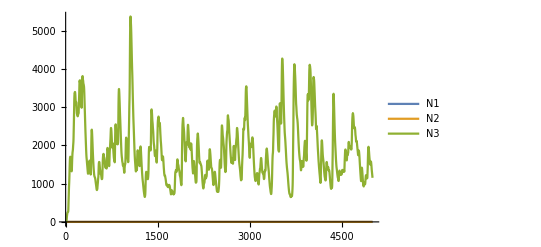

```mathematica
(* consumer 1 and 3 can coexist *)
res=Transpose[NestList[f,{X1Init,0,X3Init,N1Init,0,N3Init,0,0,0,ϵInit},plotTMax]];
ListLinePlot[res[[1;;3,1;;plotTMax]],PlotLegends->{"X1","X2","X3"}]
ListLinePlot[res[[4;;6,1;;plotTMax]],PlotLegends->{"N1","N2","N3"}]
```

```mathematica
(* average densities of seeds*)
Map[Mean[#]&, res[[1;;3]]]
(* average densities of germinants*)
Map[Mean[#]&, res[[4;;6]]]
(* variance of environmental parameter E *)
Map[Variance[#]&, res[[7;;9]]]
```

{437.678,0.,471.085}

{0.0440043,0.,1828.2}

{1.00777,0.983995,0.982169}

#### Consumers 2 and 3

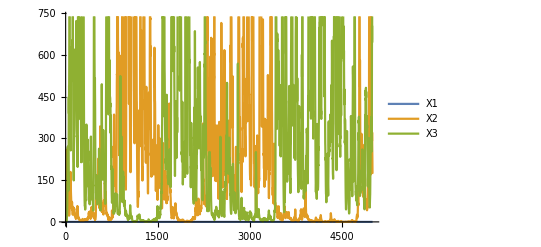

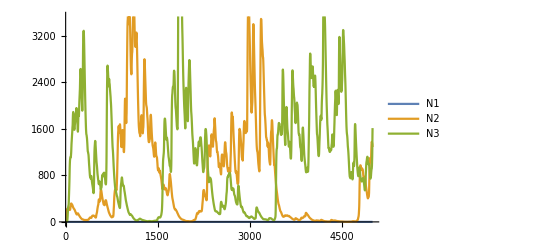

```mathematica
(* consumer 2 and 3 can coexist *)
plotTMax=5000;
res=Transpose[NestList[f,{0,X2Init,X3Init,0,N2Init,N3Init,0,0,0,ϵInit},plotTMax]];
ListLinePlot[res[[1;;3,1;;plotTMax]],PlotLegends->{"X1","X2","X3"}]
ListLinePlot[res[[4;;6,1;;plotTMax]],PlotLegends->{"N1","N2","N3"}]
```

```mathematica
(* average densities of seeds*)
Map[Mean[#]&, res[[1;;3]]]
(* average densities of germinants*)
Map[Mean[#]&, res[[4;;6]]]
(* variance of environmental parameter E *)
Map[Variance[#]&, res[[7;;9]]]
```

{0.,194.293,284.099}

{0.,747.682,1094.54}

{1.03016,0.990179,1.10538}

## Calculating generation time and sensitivity to competition

### Function for generating the sensitivity to competition, β_j^(1)

```mathematica
(* transition probability matrix, uses the definition C_j = α_{j1}F1 + α_{j2}F2 + α_{j3}F3, which leads to Subscript[β, j]^(1) in SI Appendix 3*)
M={{s(1-G)+G  Exp[e] / (1+c), Exp[e] / (1+c)},{G sN, sN}};
(* fecundity and survival matrixes *)
F={{G  Exp[e] / (1+c),  Exp[e] / (1+c)},{0, 0}};
S={{s(1-G),0},{G sN, sN}};
```

```mathematica
(* alternative parameterization from Appendix 3, which leads to  Subscript[β, j]^(2)*)
(*(* transition probability matrix, uses the definition C_j = Log[1 + α_{j1}F1 + α_{j2}F2 + α_{j3}F3], which leads to Subscript[β, j]^(1) in SI Appendix 3 *)
M={{s(1-G)+G  Exp[e] / Exp[c], Exp[e] / Exp[c]},{G sN, sN}};
(* fecundity and survival matrixes *)
F={{G  Exp[e] / Exp[c],  Exp[e] /Exp[c]},{0, 0}};
S={{s(1-G),0},{G sN, sN}};*)
```

```mathematica
(* get the equilbirium parameters: find the dominant eigenvalue, fix E_j^* at μ, and use the constraint (dominant eigenvalue = 1) to solve for C_j^* *)
eVals = Eigenvalues[M]
```

{(ⅇ^e G+s+c s-G s-c G s+sN+c sN-√((-ⅇ^e G-s-c s+G s+c G s-sN-c sN)^2-4 (s sN+2 c s sN+c^2 s sN-G s sN-2 c G s sN-c^2 G s sN)))/(2 (1+c)),(ⅇ^e G+s+c s-G s-c G s+sN+c sN+√((-ⅇ^e G-s-c s+G s+c G s-sN-c sN)^2-4 (s sN+2 c s sN+c^2 s sN-G s sN-2 c G s sN-c^2 G s sN)))/(2 (1+c))}

```mathematica
(* visual inspection shows second eigenvalue is dominant *)
λ0=eVals[[2]];
```

```mathematica
(* get equilibrium competition parameter *)
cSol =Solve[(λ0/.e->μ)== 1,c][[1]]
```

{c→-(-1+ⅇ^μ G+s-G s+sN-s sN+G s sN)/((1-s+G s) (-1+sN))}

```mathematica
(* the sensitivity to competition, β, is the derivative of logarithm of the dominant lyampunov exponent with respect to the competition parameter, evaluated at equilbirium *)
beta=D[Log[λ0],c]/.Flatten[{e->μ,cSol}]//Simplify
```

((1+(-1+G) s) (-1+sN))/(√((ⅇ^(2 μ) (G+(-1+G) G s sN)^2)/((1+(-1+G) s)^2 (-1+sN)^2)))

```mathematica
(* function for generating the absolute value of β *)
absBetaFunc[G_,s_,sN_,μ_]:=Evaluate[Abs[beta]]
```

```mathematica
(* test *)
absBetaFunc[G1,s1,sN1,μ1]
```

0.00660408

### function for generating the generation time

```mathematica
(* calculate right and left eigenvectors, normalize to get stable stage distribution and reproductive values respectively *)
w0=Eigenvectors[M][[2]];
w0 =w0/Total[w0];
w0={w0}//Transpose//Simplify (*transform from row vector to column vector*)

v0=Eigenvectors[Transpose[M]][[2]];
v0 =v0/Total[v0];
v0={v0}//Transpose//Simplify
```

{{(ⅇ^e G+s+c s-G s-c G s-sN-c sN+√(ⅇ^(2 e) G^2-2 (1+c) ⅇ^e G ((-1+G) s-sN)+(1+c)^2 ((-1+G) s+sN)^2))/(ⅇ^e G+s+c s-G s-c G s-sN-c sN+2 G sN+2 c G sN+√(ⅇ^(2 e) G^2-2 (1+c) ⅇ^e G ((-1+G) s-sN)+(1+c)^2 ((-1+G) s+sN)^2))},{(2 (1+c) G sN)/(ⅇ^e G+s+c s-G s-c G s-sN-c sN+2 G sN+2 c G sN+√(ⅇ^(2 e) G^2-2 (1+c) ⅇ^e G ((-1+G) s-sN)+(1+c)^2 ((-1+G) s+sN)^2))}}

{{(ⅇ^e G+s+c s-G s-c G s-sN-c sN+√(ⅇ^(2 e) G^2-2 (1+c) ⅇ^e G ((-1+G) s-sN)+(1+c)^2 ((-1+G) s+sN)^2))/(2 ⅇ^e+ⅇ^e G+s+c s-G s-c G s-sN-c sN+√(ⅇ^(2 e) G^2-2 (1+c) ⅇ^e G ((-1+G) s-sN)+(1+c)^2 ((-1+G) s+sN)^2))},{(2 ⅇ^e)/(2 ⅇ^e+ⅇ^e G+s+c s-G s-c G s-sN-c sN+√(ⅇ^(2 e) G^2-2 (1+c) ⅇ^e G ((-1+G) s-sN)+(1+c)^2 ((-1+G) s+sN)^2))}}

```mathematica
(* generation time (GT) is the weighted mean age of parents of all births at one point in time,  with weights given by offspring reproductive values *)
GT=((λ0 *Transpose[v0].w0)/(Transpose[v0].F.w0)/.Flatten[{e->μ,cSol}])[[1,1]]//FullSimplify
```

(ⅇ^μ G (1+(-1+G) s sN)^2+(1+(-1+G) s) (-1+sN) √((ⅇ^(2 μ) (G+(-1+G) G s sN)^2)/((1+(-1+G) s)^2 (-1+sN)^2)) (-1+(2+(-1+G) s) sN))/((1+(-1+G) s) (-1+sN) ((1+(-1+G) s) (-1+sN) √((ⅇ^(2 μ) (G+(-1+G) G s sN)^2)/((1+(-1+G) s)^2 (-1+sN)^2))+ⅇ^μ G (-1+(2+(-1+G) s) sN)))

Unlike the sensitivity to competition, the generation time does not depend on the mean of the environmental parameter, μ. Even though we have derived the generation time with the (E_j, C_j) parameterization, the generation time is the same, regardless of what parameterization we use (C_j vs \boldsymbol{F}) or the definition of C_j.

```mathematica
(* Compare the simplified formulas for generation time and 1/Abs[beta] *)
$Assumptions=e>0&& c>0&&μ>0&&s>0&&s<1&&sN>0&&sN<1&&G>0&&G<1;
Assuming[$Assumptions, FullSimplify[GT]]
Assuming[$Assumptions, FullSimplify[1/Abs[beta]]]
```

-(1+(-1+G) s sN)/((1+(-1+G) s) (-1+sN))

(ⅇ^μ G (1+(-1+G) s sN))/((1+(-1+G) s)^2 (-1+sN)^2)

```mathematica
(* function for generation time*)
GTFunc[G_,s_,sN_,μ_]:=Evaluate[GT]
(* test *)
GTFunc[G1,s1,sN1,μ1]
```

5.26416

## Get sensitivities to the determinants of the per-capita growth rate: Fix E at it’s temporal mean, 0, and then solve for the equilibrium competition parameter

```mathematica
(* function PCGR = per capita growth rate; parameterized in terms of E and C *)
PCGR[e_,c_,G_,s_, sN_]:=Evaluate[λ0]
```

```mathematica
(* instantiate equilbirium parameters. *)
EStar=ConstantArray[0,3];
CStar=ConstantArray[0,3];
```

```mathematica
(* Fix the equilbirium environmental parameter at the temporal average of E *)
EStar[[1]]=μ1;
EStar[[2]]=μ2;
EStar[[3]]=μ3;
```

```mathematica
(* solve for the equilbrium competition parameters *)
CStar[[1]]=C/.Solve[PCGR[EStar[[1]],C,G1,s1, sN1] ==1,C][[1]];
CStar[[2]]=C/.Solve[PCGR[EStar[[2]],C,G2,s2, sN2] ==1,C][[1]];
CStar[[3]]=C/.Solve[PCGR[EStar[[3]],C,G3,s3, sN3] ==1,C][[1]];
```

```mathematica
(* function gives all elements of a list for which all elements are positive *)
noZeros[a_]:=AllTrue[a,TrueQ[#>0.01]&]
```

```mathematica
(* find the feasible equilibrium of population densities *)
solAll=NSolve[{
X1tp1[{X1,X2,X3,N1,N2,N3,μ1,μ2,μ3, ϵInit}]==X1,N1tp1[{X1,X2,X3,N1,N2,N3,μ1,μ2,μ3, ϵInit}]==N1,
X2tp1[{X1,X2,X3,N1,N2,N3,μ1,μ2,μ3, ϵInit}]==X2,N2tp1[{X1,X2,X3,N1,N2,N3,μ1,μ2,μ3, ϵInit}]==N2,
X3tp1[{X1,X2,X3,N1,N2,N3,μ1,μ2,μ3, ϵInit}]==X3,N3tp1[{X1,X2,X3,N1,N2,N3,μ1,μ2,μ3, ϵInit}]==N3},
{X1,X2,X3,N1,N2,N3}];
numAll={X1,X2,X3}/.solAll//Re; (* germinant densities are exclued in case some species are annuals *)
posAll= First[Position[Map[noZeros[#]&,numAll],True]][[1]]; (* position of the equilibrium where all species have positive density *)
{X1,X2,X3,N1,N2,N3}/.solAll[[posAll]]//Re (* displays the positive equilbirium *)
```

{265.902,143.479,143.479,0.0266168,559.569,559.569}

```mathematica
(* equilibrium values for individual limiting factors (i.e. species densities), keep EStar = 0 as the equilibrium environmental variable for each species *)
FStar=ConstantArray[0,{3,3}];
FStar[[1,1]]=FStar[[2,1]]=FStar[[3,1]]=G1 X1 + N1/.solAll[[posAll]]//Re;
FStar[[1,2]]=FStar[[2,2]]=FStar[[3,2]]=G2 X2 + N2/.solAll[[posAll]]//Re;
FStar[[1,3]]=FStar[[2,3]]=FStar[[3,3]]=G3 X3 + N3/.solAll[[posAll]]//Re;
```

```mathematica
(* species responses to individual limiting factors -- used to calculate the scaling factors *)
PCGR[e_,c_,G_,s_, sN_]:=Evaluate[λ0]
prePhiF=D[{
Log[PCGR[EStar[[1]],A[[1,1]]F1+A[[1,2]]F2+A[[1,3]] F3,G1,s1, sN1]],
Log[PCGR[EStar[[2]],A[[2,1]]F1+A[[2,2]]F2+A[[2,3]] F3,G2,s2, sN2]],
Log[PCGR[EStar[[3]],A[[3,1]]F1+A[[3,2]]F2+A[[3,3]] F3,G3,s3, sN3]]},{{F1,F2,F3}}];
PhiF=Table[prePhiF[[i]]/.{F1->FStar[[i,1]],F2->FStar[[i,2]],F3->FStar[[i,3]]},{i,1,3}];
PhiF//MatrixForm
```

(-0.00660408 | -6.60408×10^-6 | -6.60408×10^-6
-1.9655×10^-8 | -0.000019655 | -0.0000196747
-1.9655×10^-8 | -0.0000196747 | -0.000019655)

## Functions for calculating intermediate quantities for exact coexistence mechanisms

```mathematica
Xtp1[{X_,N_,e_,c_,G_,s_, sN_}]:= X s(1-G) + (X G + N) * Exp[e] / (1+c);
Ntp1[{X_,N_,e_,c_,G_,s_, sN_}]:= (X G +N) sN;
```

```mathematica
PCGRFunc[E_,C_]:=Table[
pastPop = {XVecs[[i,j]],NVecs[[i,j]]};
If[j == invIndex, pastPop  = pastPop*initDens/Norm[pastPop];];
nextX=Xtp1[{pastPop[[1]],pastPop[[2]],E[[i,j]],C[[i,j]],GVec[[j]],sVec[[j]], sNVec[[j]]}];
nextN=Ntp1[{pastPop[[1]],pastPop[[2]],E[[i,j]],C[[i,j]],GVec[[j]],sVec[[j]], sNVec[[j]]}];
Log[(nextX+nextN)/(pastPop[[1]]+pastPop[[2]])],
{i,burnIn,tMax},{j,1,3}];
```

## get intermediate quantities for invader-invader comparison- where all species are at typical densities

```mathematica
(* simulation parameters *)
X1Init=1;
X2Init=1;
X3Init =1;
N1Init=1;
N2Init=1;
N3Init =1;
plotTMax = 500;
```

```mathematica
res=Transpose[NestList[f,{X1Init,X2Init,X3Init,N1Init,N2Init,N3Init,μ1,μ2,μ3, ϵInit},tMax]];
```

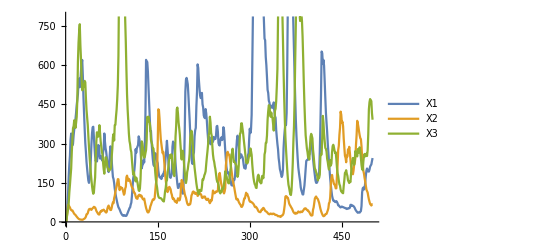

```mathematica
ListLinePlot[res[[1;;3,1;;plotTMax]],PlotLegends->{"X1","X2","X3"}]
```

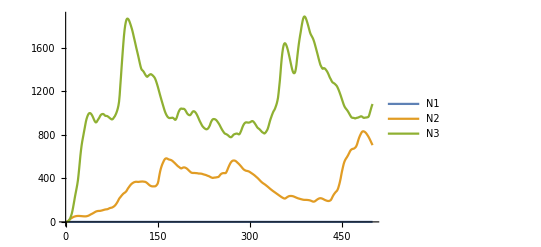

```mathematica
ListLinePlot[res[[4;;6,1;;plotTMax]],PlotLegends->{"N1","N2","N3"}]
```

```mathematica
XVecs = Table[{res[[1,i]],res[[2,i]],res[[3,i]]},{i,1,tMax}];
NVecs = Table[{res[[4,i]],res[[5,i]],res[[6,i]]},{i,1,tMax}];
FVecs = Table[{(res[[1,i]]G1+res[[4,i]]),(res[[2,i]]G2+res[[5,i]]),(res[[3,i]]G3+res[[6,i]])},{i,1,tMax}];
(* temporal average of species densities *)
FBarHigh=Mean[FVecs];
CVecs = Table[A[[j,1]]*(res[[1,i]]G1+res[[4,i]])+A[[j,2]]*(res[[2,i]]G2+res[[5,i]])+A[[j,3]]*(res[[3,i]]G3+res[[6,i]]),{i,1,tMax},{j,1,3}];
EVecs = Table[res[[j,i]],{i,1,tMax},{j,7,9}];
(* temporal average of the competition parameters *)
CBarHigh=Mean[CVecs[[burnIn;;tMax,;;]]];
(* temporal average of the environmental parameters *)
EBarHigh=Map[Mean[#[[burnIn;;tMax]]]&, res[[7;;9]]];
(* temporal variance of the competition parameter *)
CVarHigh=Table[Covariance[CVecs[[burnIn;;tMax,i]],CVecs [[burnIn;;tMax,j]]],{i,1,3},{j,1,3}];
(* temporal variance of the environmental parameter *)
EVarHigh=Table[Covariance[EVecs[[burnIn;;tMax,i]],EVecs [[burnIn;;tMax,j]]],{i,1,3},{j,1,3}];
(* temporal covariance between the environment and competition *)
CECovHigh=Table[Covariance[CVecs[[burnIn;;tMax,i]],EVecs [[burnIn;;tMax,j]]],{i,1,3},{j,1,3}];
```

```mathematica
(* long-term average per-capita growth rate of each species *)
avgGRHigh=Mean[PCGRFunc[EVecs,CVecs]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the competition parameter at its equilibrium value *)
avgGRCStarHigh=Mean[PCGRFunc[EVecs,ConstantArray[CStar,tMax]]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the environmental parameter at its equilibrium value *)
avgGREStarHigh=Mean[PCGRFunc[ConstantArray[EStar,tMax],CVecs]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the environmental parameter at its equilibrium value, and the competition parameter at its temporal average *)
avgGREStarCBarHigh=Mean[PCGRFunc[ConstantArray[EStar,tMax],ConstantArray[CBarHigh,tMax]]]
```

{0.0000585143,0.000103379,-0.00173383}

{0.0829734,0.0220492,0.0180344}

{0.0108519,-0.0115303,-0.0106153}

{-0.081859,-0.0155831,-0.0146064}

## Invasion analysis: species 1 is the invader

```mathematica
(* simulation parameters *)
X1Init=0;
X2Init=1;
X3Init =1;
N1Init=0;
N2Init=1;
N3Init =1;
plotTMax = 5000;
```

```mathematica
res=Transpose[NestList[f,{X1Init,X2Init,X3Init,N1Init,N2Init,N3Init,μ1,μ2,μ3, ϵInit},tMax]];
```

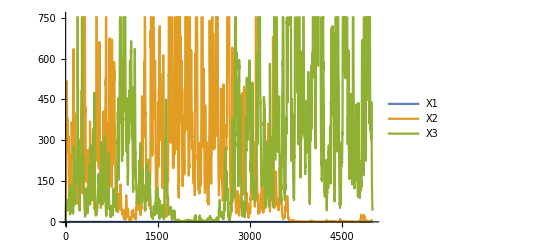

```mathematica
ListLinePlot[res[[1;;3,1;;plotTMax]],PlotLegends->{"X1","X2","X3"}]
```

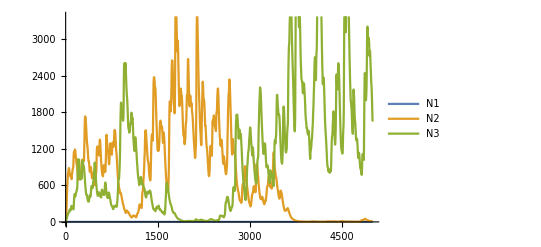

```mathematica
ListLinePlot[res[[4;;6,1;;plotTMax]],PlotLegends->{"N1","N2","N3"}]
```

```mathematica
XVecs = Table[{res[[1,i]],res[[2,i]],res[[3,i]]},{i,1,tMax}];
NVecs = Table[{res[[4,i]],res[[5,i]],res[[6,i]]},{i,1,tMax}];
FVecs = Table[{(res[[1,i]]G1+res[[4,i]]),(res[[2,i]]G2+res[[5,i]]),(res[[3,i]]G3+res[[6,i]])},{i,1,tMax}];
(* temporal average of species densities *)
FBar1=Mean[FVecs];
CVecs = Table[A[[j,1]]*(res[[1,i]]G1+res[[4,i]])+A[[j,2]]*(res[[2,i]]G2+res[[5,i]])+A[[j,3]]*(res[[3,i]]G3+res[[6,i]]),{i,1,tMax},{j,1,3}];
EVecs = Table[res[[j,i]],{i,1,tMax},{j,7,9}];
(* temporal average of the competition parameters *)
CBar1=Mean[CVecs[[burnIn;;tMax,;;]]];
(* temporal average of the environmental parameters *)
EBar1=Map[Mean[#[[burnIn;;tMax]]]&, res[[7;;9]]];
(* temporal variance of the competition parameter *)
CVar1=Table[Covariance[CVecs[[burnIn;;tMax,i]],CVecs [[burnIn;;tMax,j]]],{i,1,3},{j,1,3}];
(* temporal variance of the environmental parameter *)
EVar1=Table[Covariance[EVecs[[burnIn;;tMax,i]],EVecs [[burnIn;;tMax,j]]],{i,1,3},{j,1,3}];
(* temporal covariance between the environment and competition *)
CECov1=Table[Covariance[CVecs[[burnIn;;tMax,i]],EVecs [[burnIn;;tMax,j]]],{i,1,3},{j,1,3}];
```

```mathematica
invIndex = 1;
XVecs[[1,invIndex]] =initDens; 
NVecs[[1,invIndex]] =initDens;
```

```mathematica
Table[{
pastPop = {XVecs[[i,invIndex]],NVecs[[i,invIndex]]};
pastPop  = pastPop*initDens/Norm[pastPop];
XVecs[[i+1,invIndex]]=Xtp1[{pastPop[[1]],pastPop[[2]],EVecs[[i,invIndex]],CVecs[[i,invIndex]],GVec[[invIndex]],sVec[[invIndex]], sNVec[[invIndex]]}];
NVecs[[i+1,invIndex]]=Ntp1[{pastPop[[1]],pastPop[[2]],EVecs[[i,invIndex]],CVecs[[i,invIndex]],GVec[[invIndex]],sVec[[invIndex]], sNVec[[invIndex]]}];},
{i,1,tMax}];
```

Set::partw: Part 10001 of {{0.001,1,1},{0.0429469,19.5717,19.5717},{0.00623791,39.275,39.275},{0.00596558,65.672,51.1546},{0.00506419,103.292,58.6584},{0.00646387,142.856,57.5079},«40»,{0.00435835,300.428,46.6602},{0.00351654,297.753,46.7819},{0.00310638,297.559,47.2401},{0.00261373,313.442,47.8407},«9950»} does not exist.

Set::partw: Part 10001 of {{0.001,1,1},{7.77817×10^-7,1.0725,1.0725},{1.00018×10^-7,2.95392,2.95392},{1.00016×10^-7,6.70939,6.70939},{1.00017×10^-7,12.9447,11.5292},{1.0002×10^-7,22.692,16.9602},«40»,{1.00036×10^-7,842.718,148.836},{1.00023×10^-7,850.941,149.665},{1.00028×10^-7,858.699,150.484},{1.00032×10^-7,866.243,151.328},«9950»} does not exist.

```mathematica
(* long-term average per-capita growth rate of each species *)
avgGR1=Mean[PCGRFunc[EVecs,CVecs]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the competition parameter at its equilibrium value *)
avgGRCStar1=Mean[PCGRFunc[EVecs,ConstantArray[CStar,tMax]]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the environmental parameter at its equilibrium value *)
avgGREStar1=Mean[PCGRFunc[ConstantArray[EStar,tMax],CVecs]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the environmental parameter at its equilibrium value, and the competition parameter at its temporal average *)
avgGREStarCBar1=Mean[PCGRFunc[ConstantArray[EStar,tMax],ConstantArray[CBar1,tMax]]]
```

{1.08146,-0.000346266,-0.0000185403}

{0.0685329,0.0188857,0.0230356}

{0.995847,-0.011619,-0.0117787}

{0.961415,-0.0149827,-0.0154816}

```mathematica
(* scaling factors *)
preQ = Drop[PhiF[[1]],{1}].PseudoInverse[Drop[PhiF,{1},{1}]];
q1 = Insert[-preQ,1,1]//N
(* the simple comparison *)
noQ1 = {1,-1/2,-1/2}//N
(* generation time scaling *)
GTS1= {1,-GTFunc[G2,s2,sN2,μ2]/(2*GTFunc[G1,s1,sN1,μ1]),-GTFunc[G3,s3,sN3,μ3]/(2*GTFunc[G1,s1,sN1,μ1])}//N
(* chesson 2018 method *)
BS1= {1,-absBetaFunc[G1,s1,sN1,μ1]/(2*absBetaFunc[G2,s2,sN2,μ2]),-absBetaFunc[G1,s1,sN1,μ1]/(2*absBetaFunc[G3,s3,sN3,μ3]) }//N
```

{1.,-0.167916,-0.167916}

{1.,-0.5,-0.5}

{1.,-4.2042,-4.2042}

{1.,-168.,-168.}

## Invasion analysis: species 2 is the invader

```mathematica
(* simulation parameters *)
X1Init=1;
X2Init=0;
X3Init =1;
N1Init=1;
N2Init=0;
N3Init =1;
plotTMax = 5000;
```

```mathematica
res=Transpose[NestList[f,{X1Init,X2Init,X3Init,N1Init,N2Init,N3Init,μ1,μ2,μ3, ϵInit},tMax]];
```

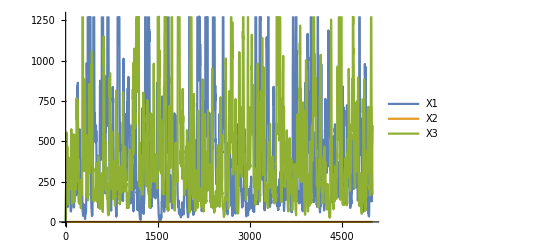

```mathematica
ListLinePlot[res[[1;;3,1;;plotTMax]],PlotLegends->{"X1","X2","X3"}]
```

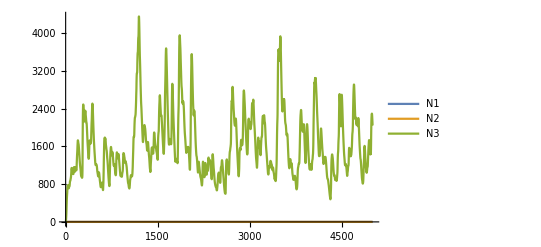

```mathematica
ListLinePlot[res[[4;;6,1;;plotTMax]],PlotLegends->{"N1","N2","N3"}]
```

```mathematica
XVecs = Table[{res[[1,i]],res[[2,i]],res[[3,i]]},{i,1,tMax}];
NVecs = Table[{res[[4,i]],res[[5,i]],res[[6,i]]},{i,1,tMax}];
FVecs = Table[{(res[[1,i]]G1+res[[4,i]]),(res[[2,i]]G2+res[[5,i]]),(res[[3,i]]G3+res[[6,i]])},{i,1,tMax}];
(* temporal average of species densities *)
FBar2=Mean[FVecs];
CVecs = Table[A[[j,1]]*(res[[1,i]]G1+res[[4,i]])+A[[j,2]]*(res[[2,i]]G2+res[[5,i]])+A[[j,3]]*(res[[3,i]]G3+res[[6,i]]),{i,1,tMax},{j,1,3}];
EVecs = Table[res[[j,i]],{i,1,tMax},{j,7,9}];
(* temporal average of the competition parameters *)
CBar2=Mean[CVecs[[burnIn;;tMax,;;]]];
(* temporal average of the environmental parameters *)
EBar2=Map[Mean[#[[burnIn;;tMax]]]&, res[[7;;9]]];
(* temporal variance of the competition parameter *)
CVar2=Table[Covariance[CVecs[[burnIn;;tMax,i]],CVecs [[burnIn;;tMax,j]]],{i,1,3},{j,1,3}];
(* temporal variance of the environmental parameter *)
EVar2=Table[Covariance[EVecs[[burnIn;;tMax,i]],EVecs [[burnIn;;tMax,j]]],{i,1,3},{j,1,3}];
(* temporal covariance between the environment and competition *)
CECov2=Table[Covariance[CVecs[[burnIn;;tMax,i]],EVecs [[burnIn;;tMax,j]]],{i,1,3},{j,1,3}];
```

```mathematica
invIndex = 2;
XVecs[[1,invIndex]] =initDens; 
NVecs[[1,invIndex]] =initDens;
```

```mathematica
Table[{
pastPop = {XVecs[[i,invIndex]],NVecs[[i,invIndex]]};
pastPop  = pastPop*initDens/Norm[pastPop];
XVecs[[i+1,invIndex]]=Xtp1[{pastPop[[1]],pastPop[[2]],EVecs[[i,invIndex]],CVecs[[i,invIndex]],GVec[[invIndex]],sVec[[invIndex]], sNVec[[invIndex]]}];
NVecs[[i+1,invIndex]]=Ntp1[{pastPop[[1]],pastPop[[2]],EVecs[[i,invIndex]],CVecs[[i,invIndex]],GVec[[invIndex]],sVec[[invIndex]], sNVec[[invIndex]]}];},
{i,1,tMax}];
```

Set::partw: Part 10001 of {{1,0.001,1},{29.3941,0.0207742,29.3941},{64.5103,0.00229346,67.488},{81.519,0.00158558,130.851},{102.72,0.00117279,196.817},{156.418,0.00107917,202.688},«40»,{255.282,0.000549975,152.68},{241.524,0.000575993,153.338},{240.891,0.000529104,157.681},{252.067,0.000499389,155.167},«9950»} does not exist.

Set::partw: Part 10001 of {{1,0.001,1},{0.0011,0.000758372,1.0725},{0.00294051,0.000133004,3.91161},{0.00645397,0.000153785,10.3939},{0.00815835,0.000191168,22.892},{0.0102801,0.000253087,41.5094},«40»,{0.026195,0.000854655,723.758},{0.0255544,0.000872669,720.55},{0.0241779,0.00086744,717.487},{0.0241132,0.000883147,714.923},«9950»} does not exist.

```mathematica
(* long-term average per-capita growth rate of each species *)
avgGR2=Mean[PCGRFunc[EVecs,CVecs]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the competition parameter at its equilibrium value *)
avgGRCStar2=Mean[PCGRFunc[EVecs,ConstantArray[CStar,tMax]]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the environmental parameter at its equilibrium value *)
avgGREStar2=Mean[PCGRFunc[ConstantArray[EStar,tMax],CVecs]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the environmental parameter at its equilibrium value, and the competition parameter at its temporal average *)
avgGREStarCBar2=Mean[PCGRFunc[ConstantArray[EStar,tMax],ConstantArray[CBar2,tMax]]]
```

{-0.000164246,0.00530866,0.0000192516}

{0.0543867,0.0209496,0.0177601}

{0.0272503,-0.011685,-0.00872592}

{-0.0622144,-0.0151175,-0.0130886}

```mathematica
(* scaling factors *)
preQ = Drop[PhiF[[2]],{2}].PseudoInverse[Drop[PhiF,{2},{2}]];
q2 = Insert[-preQ,1,2]//N
(* the simple comparison *)
noQ2 = {-1/2,1,-1/2}//N
(* generation time scaling *)
GTS2= {-GTFunc[G1,s1,sN1,μ1]/(2*GTFunc[G2,s2,sN2,μ2]),1,-GTFunc[G3,s3,sN3,μ3]/(2*GTFunc[G2,s2,sN2,μ2])}//N
(* beta scaling *)
BS2= {-absBetaFunc[G2,s2,sN2,μ2]/(2*absBetaFunc[G1,s1,sN1,μ1]),1,-absBetaFunc[G2,s2,sN2,μ2]/(2*absBetaFunc[G3,s3,sN3,μ3] )}//N
```

{2.9762×10^-9,1.,-1.001}

{-0.5,1.,-0.5}

{-0.0594643,1.,-0.5}

{-0.0014881,1.,-0.5}

## Invasion analysis: species 3 is the invader

```mathematica
(* simulation parameters *)
X1Init=1;
X2Init=1;
X3Init =0;
N1Init=1;
N2Init=1;
N3Init =0;
plotTMax = 5000;
```

```mathematica
res=Transpose[NestList[f,{X1Init,X2Init,X3Init,N1Init,N2Init,N3Init,μ1,μ2,μ3, ϵInit},tMax]];
```

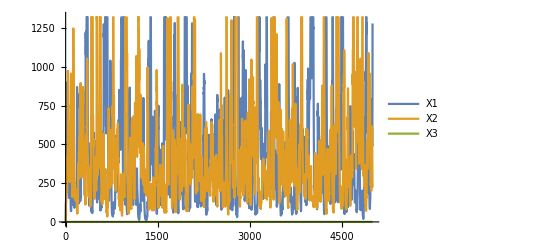

```mathematica
ListLinePlot[res[[1;;3,1;;plotTMax]],PlotLegends->{"X1","X2","X3"}]
```

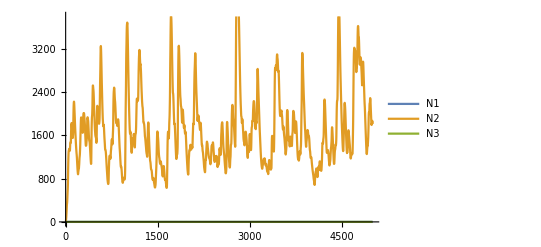

```mathematica
ListLinePlot[res[[4;;6,1;;plotTMax]],PlotLegends->{"N1","N2","N3"}]
```

```mathematica
XVecs = Table[{res[[1,i]],res[[2,i]],res[[3,i]]},{i,1,tMax}];
NVecs = Table[{res[[4,i]],res[[5,i]],res[[6,i]]},{i,1,tMax}];
FVecs = Table[{(res[[1,i]]G1+res[[4,i]]),(res[[2,i]]G2+res[[5,i]]),(res[[3,i]]G3+res[[6,i]])},{i,1,tMax}];
(* temporal average of species densities *)
FBar3=Mean[FVecs];
CVecs = Table[A[[j,1]]*(res[[1,i]]G1+res[[4,i]])+A[[j,2]]*(res[[2,i]]G2+res[[5,i]])+A[[j,3]]*(res[[3,i]]G3+res[[6,i]]),{i,1,tMax},{j,1,3}];
EVecs = Table[res[[j,i]],{i,1,tMax},{j,7,9}];
(* temporal average of the competition parameters *)
CBar3=Mean[CVecs[[burnIn;;tMax,;;]]];
(* temporal average of the environmental parameters *)
EBar3=Map[Mean[#[[burnIn;;tMax]]]&, res[[7;;9]]];
(* temporal variance of the competition parameter *)
CVar3=Table[Covariance[CVecs[[burnIn;;tMax,i]],CVecs [[burnIn;;tMax,j]]],{i,1,3},{j,1,3}];
(* temporal variance of the environmental parameter *)
EVar3=Table[Covariance[EVecs[[burnIn;;tMax,i]],EVecs [[burnIn;;tMax,j]]],{i,1,3},{j,1,3}];
(* temporal covariance between the environment and competition *)
CECov3=Table[Covariance[CVecs[[burnIn;;tMax,i]],EVecs [[burnIn;;tMax,j]]],{i,1,3},{j,1,3}];
```

```mathematica
invIndex = 3;
XVecs[[1,invIndex]] =initDens; 
NVecs[[1,invIndex]] =initDens;
```

```mathematica
Table[{
pastPop = {XVecs[[i,invIndex]],NVecs[[i,invIndex]]};
pastPop  = pastPop*initDens/Norm[pastPop];
XVecs[[i+1,invIndex]]=Xtp1[{pastPop[[1]],pastPop[[2]],EVecs[[i,invIndex]],CVecs[[i,invIndex]],GVec[[invIndex]],sVec[[invIndex]], sNVec[[invIndex]]}];
NVecs[[i+1,invIndex]]=Ntp1[{pastPop[[1]],pastPop[[2]],EVecs[[i,invIndex]],CVecs[[i,invIndex]],GVec[[invIndex]],sVec[[invIndex]], sNVec[[invIndex]]}];},
{i,1,tMax}];
```

Set::partw: Part 10001 of {{1,1,0.001},{29.3941,29.3941,0.0207742},{64.5103,67.488,0.00229346},{83.6062,116.059,0.0017209},{112.739,116.82,0.00214973},{133.214,123.964,0.00159631},«40»,{206.67,551.774,0.000280148},{205.624,490.604,0.000310241},{205.258,453.085,0.000323555},{221.743,394.789,0.000345859},«9950»} does not exist.

Set::partw: Part 10001 of {{1,1,0.001},{0.0011,1.0725,0.000758372},{0.00294051,3.91161,0.000133004},{0.00645397,10.3939,0.000153785},{0.00836707,21.4498,0.000183896},{0.0112823,32.3035,0.000180247},«40»,{0.0205718,1262.54,0.000964143},{0.0206875,1284.77,0.000963481},{0.0205831,1300.49,0.000957957},{0.0205464,1312.15,0.000954933},«9950»} does not exist.

```mathematica
(* long-term average per-capita growth rate of each species *)
avgGR3=Mean[PCGRFunc[EVecs,CVecs]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the competition parameter at its equilibrium value *)
avgGRCStar3=Mean[PCGRFunc[EVecs,ConstantArray[CStar,tMax]]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the environmental parameter at its equilibrium value *)
avgGREStar3=Mean[PCGRFunc[ConstantArray[EStar,tMax],CVecs]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the environmental parameter at its equilibrium value, and the competition parameter at its temporal average *)
avgGREStarCBar3=Mean[PCGRFunc[ConstantArray[EStar,tMax],ConstantArray[CBar3,tMax]]]
```

{0.000348889,-0.0000762351,0.00157116}

{0.0758119,0.0204905,0.0167604}

{0.00891849,-0.00984202,-0.0107946}

{-0.0747522,-0.0145576,-0.0147431}

```mathematica
(* scaling factors *)
preQ = Drop[PhiF[[3]],{3}].PseudoInverse[Drop[PhiF,{3},{3}]];
q3= Insert[-preQ,1,3]//N
(* the simple comparison *)
noQ3 = {-1/2,-1/2,1}//N
(* generation time scaling *)
GTS3= {-GTFunc[G1,s1,sN1,μ1]/(2*GTFunc[G3,s3,sN3,μ3]),-GTFunc[G2,s2,sN2,μ2]/(2*GTFunc[G3,s3,sN3,μ3]),1}//N
(* beta scaling *)
BS3= {-absBetaFunc[G3,s3,sN3,μ3]/(2*absBetaFunc[G1,s1,sN1,μ1]),-absBetaFunc[G3,s3,sN3,μ3]/(2*absBetaFunc[G2,s2,sN2,μ2]),1 }//N
```

{2.9762×10^-9,-1.001,1.}

{-0.5,-0.5,1.}

{-0.0594643,-0.5,1.}

{-0.0014881,-0.5,1.}

## Functions for computing coexistence mechansisms

### Invader-resident comparisons

#### exact

```mathematica
(* regular exact coexistence mechansism - used with scaling factors *)
deltaEE[q_, avgGRCStar_]:=q.(avgGRCStar)
rPrimeE[q_, avgGRCStar_, avgGREStarCBar_ ,Phi_, CStar_]:=q.(avgGRCStar)- q.Total[Phi*CStar ,{2}]
rPrimeE[q_, avgGRCStar_, avgGREStarCBar_]:=q.(avgGRCStar)+q.(avgGREStarCBar)
deltaRhoE[q_, avgGREStarCBar_,Phi_, CStar_]:=q.(avgGREStarCBar)+ q.Total[Phi*CStar ,{2}]
deltaRhoE[q_, avgGREStarCBar_,Phi_, CStar_]:=0
deltaRhoENew[q_, avgGREStarCBar_]:=q.(avgGREStarCBar)
deltaNE[q_,avgGREStar_,avgGREStarCBar_]:=q.(avgGREStar-avgGREStarCBar)
deltaIE[q_,avgGREStar_,avgGRCStar_,avgGR_]:=q.(avgGR-avgGREStar-avgGRCStar)
```

### Invader-invader comparisons

#### exact

```mathematica
(* regular exact coexistence mechansism - used with scaling factors *)
deltaEEII[ avgGRCStarLow_, avgGRCStarHigh_, spInd_]:=(avgGRCStarLow[[spInd]])-(avgGRCStarHigh[[spInd]])
deltaRhoEII[avgGREStarCBarLow_,avgGREStarCBarHigh_, spInd_]:=(avgGREStarCBarLow[[spInd]])-(avgGREStarCBarHigh[[spInd]])
deltaNEII[avgGREStarLow_,avgGREStarCBarLow_,avgGREStarHigh_,avgGREStarCBarHigh_, spInd_]:=(avgGREStarLow[[spInd]]-avgGREStarCBarLow[[spInd]])-(avgGREStarHigh[[spInd]]-avgGREStarCBarHigh[[spInd]])
deltaIEII[avgGREStarLow_,avgGRCStarLow_,avgGRLow_,avgGREStarHigh_,avgGRCStarHigh_,avgGRHigh_, spInd_]:=(avgGRLow[[spInd]]-avgGREStarLow[[spInd]]-avgGRCStarLow[[spInd]])-(avgGRHigh[[spInd]]-avgGREStarHigh[[spInd]]-avgGRCStarHigh[[spInd]])
```

## Tables of exact coexistence mechanisms

```mathematica
names = {Δθ,ΔN,ΔI};
spInd = 1;
T1={
{deltaEE[q1, avgGRCStar1]+deltaRhoENew[q1, avgGREStarCBar1],deltaNE[q1,avgGREStar1,avgGREStarCBar1],deltaIE[q1,avgGREStar1,avgGRCStar1,avgGR1] },

{deltaEE[noQ1, avgGRCStar1]+deltaRhoENew[noQ1, avgGREStarCBar1],deltaNE[noQ1,avgGREStar1,avgGREStarCBar1],deltaIE[noQ1,avgGREStar1,avgGRCStar1,avgGR1] },

{deltaEE[GTS1, avgGRCStar1]+deltaRhoENew[GTS1, avgGREStarCBar1],deltaNE[GTS1,avgGREStar1,avgGREStarCBar1],deltaIE[GTS1,avgGREStar1,avgGRCStar1,avgGR1]},

{ deltaEE[BS1, avgGRCStar1]+deltaRhoENew[BS1, avgGREStarCBar1],deltaNE[BS1,avgGREStar1,avgGREStarCBar1],deltaIE[BS1,avgGREStar1,avgGRCStar1,avgGR1]},

{deltaEEII[ avgGRCStar1, avgGRCStarHigh, spInd]+deltaRhoEII[avgGREStarCBar1,avgGREStarCBarHigh, spInd],deltaNEII[avgGREStar1,avgGREStarCBar1,avgGREStarHigh,avgGREStarCBarHigh, spInd],deltaIEII[avgGREStar1,avgGRCStar1,avgGR1,avgGREStarHigh,avgGRCStarHigh,avgGRHigh, spInd]}};
```

```mathematica
NumberForm[MatrixForm[Prepend[T1,names]],{3,4}]
```

(Δθ | ΔN | ΔI
1.0300 | 0.0332 | 0.0203
1.0200 | 0.0309 | 0.0265
0.9820 | 0.0047 | 0.0965
-0.8950 | -1.1500 | 3.1900
1.0300 | -0.0583 | 0.1110)

```mathematica
names = {Δθ,ΔN,ΔI};
spInd = 2;
T2={
{deltaEE[q2, avgGRCStar2]+deltaRhoENew[q2, avgGREStarCBar2],deltaNE[q2,avgGREStar2,avgGREStarCBar2],deltaIE[q2,avgGREStar2,avgGRCStar2,avgGR2] },

{deltaEE[noQ2, avgGRCStar2]+deltaRhoENew[noQ2, avgGREStarCBar2],deltaNE[noQ2,avgGREStar2,avgGREStarCBar2],deltaIE[noQ2,avgGREStar2,avgGRCStar2,avgGR2] },

{deltaEE[GTS2, avgGRCStar2]+deltaRhoENew[GTS2, avgGREStarCBar2],deltaNE[GTS2,avgGREStar2,avgGREStarCBar2],deltaIE[GTS2,avgGREStar2,avgGRCStar2,avgGR2]},

{ deltaEE[BS2, avgGRCStar2]+deltaRhoENew[BS2, avgGREStarCBar2],deltaNE[BS2,avgGREStar2,avgGREStarCBar2],deltaIE[BS2,avgGREStar2,avgGRCStar2,avgGR2]},

{deltaEEII[ avgGRCStar2, avgGRCStarHigh, spInd]+deltaRhoEII[avgGREStarCBar2,avgGREStarCBarHigh, spInd],deltaNEII[avgGREStar2,avgGREStarCBar2,avgGREStarHigh,avgGREStarCBarHigh, spInd],deltaIEII[avgGREStar2,avgGRCStar2,avgGR2,avgGREStarHigh,avgGRCStarHigh,avgGRHigh, spInd]}};
NumberForm[MatrixForm[Prepend[T2,names]],{3,4}]
```

(Δθ | ΔN | ΔI
0.0012 | -0.0009 | 0.0051
0.0074 | -0.0435 | 0.0415
0.0040 | -0.0041 | 0.0054
0.0035 | 0.0011 | 0.0007
-0.0006 | -0.0006 | 0.0065)

```mathematica
names = {Δθ,ΔN,ΔI};
spInd = 3;
T3={
{deltaEE[q3, avgGRCStar3]+deltaRhoENew[q3, avgGREStarCBar3],deltaNE[q3,avgGREStar3,avgGREStarCBar3],deltaIE[q3,avgGREStar3,avgGRCStar3,avgGR3] },

{deltaEE[noQ3, avgGRCStar3]+deltaRhoENew[noQ3, avgGREStarCBar3],deltaNE[noQ3,avgGREStar3,avgGREStarCBar3],deltaIE[noQ3,avgGREStar3,avgGRCStar3,avgGR3] },

{deltaEE[GTS3, avgGRCStar3]+deltaRhoENew[GTS3, avgGREStarCBar3],deltaNE[GTS3,avgGREStar3,avgGREStarCBar3],deltaIE[GTS3,avgGREStar3,avgGRCStar3,avgGR3]},

{ deltaEE[BS3, avgGRCStar3]+deltaRhoENew[BS3, avgGREStarCBar3],deltaNE[BS3,avgGREStar3,avgGREStarCBar3],deltaIE[BS3,avgGREStar3,avgGRCStar3,avgGR3]},

{deltaEEII[ avgGRCStar3, avgGRCStarHigh, spInd]+deltaRhoEII[avgGREStarCBar3,avgGREStarCBarHigh, spInd],deltaNEII[avgGREStar3,avgGREStarCBar3,avgGREStarHigh,avgGREStarCBarHigh, spInd],deltaIEII[avgGREStar3,avgGRCStar3,avgGR3,avgGREStarHigh,avgGRCStarHigh,avgGRHigh, spInd]}};
NumberForm[MatrixForm[Prepend[T3,names]],{3,4}]
```

(Δθ | ΔN | ΔI
-0.0039 | -0.0008 | 0.0063
-0.0015 | -0.0402 | 0.0432
-0.0010 | -0.0034 | 0.0060
-0.0010 | 0.0015 | 0.0011
-0.0014 | -0.0000 | 0.0048)

### Tables in Latex format

```mathematica
method={"Scaling factors","Simple comparison","Generation time scaling","β scaling","Invader-invader comparison"};
```

```mathematica
DecimalForm[Transpose[Join[{ConstantArray["1",5]},{method},Transpose[T1]]],{10,3}]//TeXForm
```

\left(
\begin{array}{ccccc}
 1 & \text{Scaling factors} & 1.028 & 0.033 & 0.020 \\
 1 & \text{Simple comparison} & 1.024 & 0.031 & 0.027 \\
 1 & \text{Generation time scaling} & 0.982 & 0.005 & 0.096 \\
 1 & \text{$\beta $ scaling} & -0.895 & -1.153 & 3.190 \\
 1 & \text{Invader-invader comparison} & 1.029 & -0.058 & 0.111 \\
\end{array}
\right)

```mathematica
DecimalForm[Transpose[Join[{ConstantArray["2 & 3",5]},{method},Transpose[T2]]],{10,3}]//TeXForm
```

\left(
\begin{array}{ccccc}
 \text{2 $\&$ 3} & \text{Scaling factors} & 0.001 & -0.001 & 0.005 \\
 \text{2 $\&$ 3} & \text{Simple comparison} & 0.007 & -0.043 & 0.041 \\
 \text{2 $\&$ 3} & \text{Generation time scaling} & 0.004 & -0.004 & 0.005 \\
 \text{2 $\&$ 3} & \text{$\beta $ scaling} & 0.004 & 0.001 & 0.001 \\
 \text{2 $\&$ 3} & \text{Invader-invader comparison} & -0.001 & -0.001 & 0.006 \\
\end{array}
\right)

```mathematica
DecimalForm[Transpose[Join[{ConstantArray["3",5]},{method},Transpose[T3]]],{10,3}]//TeXForm
```

\left(
\begin{array}{ccccc}
 3 & \text{Scaling factors} & -0.004 & -0.001 & 0.006 \\
 3 & \text{Simple comparison} & -0.001 & -0.040 & 0.043 \\
 3 & \text{Generation time scaling} & -0.001 & -0.003 & 0.006 \\
 3 & \text{$\beta $ scaling} & -0.001 & 0.001 & 0.001 \\
 3 & \text{Invader-invader comparison} & -0.001 & -0.000 & 0.005 \\
\end{array}
\right)